# Decaimiento del Higgs a dos fotones en VDDMM

```mathematica
$LoadPhi=True;
$LoadFeynArts=True;
Needs["HighEnergyPhysics`FeynCalc`"];
```

Loading FeynCalc from /home/felipe/.Mathematica/Applications/HighEnergyPhysics

HighEnergyPhysics`FeynCalc`MemoryAvailable`MemoryAvailable::shdw: Symbol MemoryAvailable appears in multiple contexts {HighEnergyPhysics`FeynCalc`MemoryAvailable`,System`}; definitions in context HighEnergyPhysics`FeynCalc`MemoryAvailable` may shadow or be shadowed by other definitions.

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading PHI

WARNING! Your FeynArts installation is not complete or the version you have cannot be used with this version of FeynCalc.
FeynArts can be downloaded at www.feynarts.de

Loading FeynArts, see www.feynarts.de for documentation

FeynArts not found. Please install FeynArts, e.g., in
/home/felipe/.Mathematica
and reload FeynCalc
FeynArts can be downloaded from www.feynarts.de

## Definiciones

```mathematica
dm[mu_]:=DiracMatrix[mu]
dm[5]:=DiracMatrix[5]
ds[p_]:=DiracSlash[p]
mt[mu_,nu_]:=MetricTensor[mu,nu]
fv[p_,mu_]:=FourVector[p,mu]
epsilon[a_,b_,c_,d_]:=LeviCivita[a,b,c,d]
id[n_]:=IdentityMatrix[n]
sp[p_,q_]:=ScalarProduct[p,q]
li[mu_]:=LorentzIndex[mu]
prop[p_,m_]:=ds[p]+m
```

## Modelo Estandar

### Definiciones

```mathematica
q:=p-k1-k2
R:=p-k1
propW[p_,mu_,nu_]:=ⅈ*(-mt[mu,nu]+(fv[p,mu]*fv[p,nu])/MW^2)*FeynAmpDenominator[{p,MW}]
propf[p_,Mf_]:=ⅈ*prop[p,Mf]*FeynAmpDenominator[{p,Mf}]
HWW[mu_,nu_]:=ⅈ*g*MW*mt[mu,nu]
AAWW[mu_,nu_,rho_,sigma_]:=(-ⅈ*e^2)*(2*mt[mu,nu]*mt[rho,sigma]-mt[mu,rho]*mt[nu,sigma]-mt[mu,sigma]*mt[nu,rho])
AWW[p1_,p2_,p3_,mu_,nu_,rho_]:=(-ⅈ*e)*((fv[p3,mu]-fv[p2,mu])*mt[nu,rho]+(fv[p2,rho]-fv[p1,rho])*mt[mu,nu]+(fv[p1,nu]-fv[p3,nu])*mt[mu,rho])
Hff[Mf_]:=-ⅈ*(Mf*g)/(2*MW)
Att[mu_,Qf_]:=-ⅈ*e*Qf*dm[mu]
ϵA[p_,mu_]:=PolarizationVector[p,mu]
```

### Restricciones

```mathematica
onshell={sp[k1,k1]->0,sp[k2,k2]->0,sp[k1,k2]->MH^2/2};
```

## Interaccion triangulo con W

```mathematica
mHAA1=2*Simplify[Contract[HWW[alpha,alpha].propW[p,alpha,beta].AWW[-k1,-R,p,mu,rho,beta].propW[R,rho,sig].AWW[-k2,-q,R,nu,gamma,sig].propW[q,gamma,alpha].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA1=FullSimplify[mHAA1/.onshell];
```

## Interaccion de contacto con vertice AAWW

```mathematica
mHAA2=Simplify[Contract[HWW[alpha,alpha].propW[p,alpha,beta].AAWW[mu,nu,gamma,beta].propW[q,gamma,alpha].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA2=FullSimplify[mHAA2/.onshell];
```

## Interaccion triangulo con fermiones

#### Consideremos Mt, Mc, Mb, Mtau

```mathematica
mHAA3top=2*Simplify[Contract[Nc*(-1)*Hff[Mt].Tr[Contract[propf[p,Mt].propf[q,Mt].Att[nu,2/3].propf[R,Mt].Att[mu,2/3]]].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA3top=FullSimplify[mHAA3top/.onshell];
```

```mathematica
mHAA3b=2*Simplify[Contract[Nc*(-1)*Hff[Mb].Tr[Contract[propf[p,Mb].propf[q,Mb].Att[nu,-1/3].propf[R,Mb].Att[mu,-1/3]]].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA3b=FullSimplify[mHAA3b/.onshell];
```

```mathematica
mHAA3c=2*Simplify[Contract[Nc*(-1)*Hff[Mc].Tr[Contract[propf[p,Mc].propf[q,Mc].Att[nu,2/3].propf[R,Mc].Att[mu,2/3]]].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA3c=FullSimplify[mHAA3c/.onshell];
```

```mathematica
mHAA3tau=2*Simplify[Contract[(-1)*Hff[Mtau].Tr[Contract[propf[p,Mtau].propf[q,Mtau].Att[nu,1].propf[R,Mtau].Att[mu,1]]].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA3tau=FullSimplify[mHAA3tau/.onshell];
```

## Integramos cada termino

```mathematica
IHAA1=I*Simplify[PaVeReduce[OneLoop[p,MHAA1]]]/.onshell;
```

```mathematica
IHAA2=I*Simplify[PaVeReduce[OneLoop[p,MHAA2]]]/.onshell;
```

```mathematica
IHAA3top=I*Simplify[PaVeReduce[OneLoop[p,MHAA3top]]]/.onshell;
IHAA3b=I*Simplify[PaVeReduce[OneLoop[p,MHAA3b]]]/.onshell;
IHAA3c=I*Simplify[PaVeReduce[OneLoop[p,MHAA3c]]]/.onshell;
IHAA3tau=I*Simplify[PaVeReduce[OneLoop[p,MHAA3tau]]]/.onshell;
```

```mathematica
IHAAWT=1/(64*π^4)*Simplify[IHAA1+IHAA2];
```

```mathematica
IHAAtopT=4/(64*π^4)*FullSimplify[IHAA3top];
IHAAbT=4/(64*π^4)*FullSimplify[IHAA3b];
IHAAcT=4/(64*π^4)*FullSimplify[IHAA3c];
IHAAtauT=4/(64*π^4)*FullSimplify[IHAA3tau];
```

Test de Divergencias

```mathematica
div={A0[MW^2]->MW^2*Div,B0[0,MW^2,MW^2]->Div,B0[MH^2,MW^2,MW^2]->Div};
ansW1=FullSimplify[IHAA1]/.onshell;
ansW2=FullSimplify[IHAA2]/.onshell;
div1=Simplify[Coefficient[ansW1/.div,Div]]*Div;
div2=Simplify[Coefficient[ansW2/.div,Div]]*Div;
FullSimplify[div1+div2]
```

0

### Elimino las polarizaciones de los fotones

```mathematica
IHAAW=Coefficient[IHAAWT,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])
```

1/(16 MH^2 MW π^2)e^2 g (-MH^2-6 MW^2+6 MW^2 (MH^2-2 MW^2) C0[0,0,MH^2,MW^2,MW^2,MW^2]) (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]])

```mathematica
IHAAtopT=Coefficient[IHAAtopT,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])
IHAAbT=Coefficient[IHAAbT,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])
IHAAcT=Coefficient[IHAAcT,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])
IHAAtauT=Coefficient[IHAAtauT,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])
```

-(e^2 g Mt^2 Nc (-2+(MH^2-4 Mt^2) C0[0,0,MH^2,Mt^2,Mt^2,Mt^2]) (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]]))/(18 MH^2 MW π^2)

(e^2 g Mb^2 Nc (2+(4 Mb^2-MH^2) C0[0,0,MH^2,Mb^2,Mb^2,Mb^2]) (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]]))/(72 MH^2 MW π^2)

(e^2 g Mc^2 Nc (2+(4 Mc^2-MH^2) C0[0,0,MH^2,Mc^2,Mc^2,Mc^2]) (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]]))/(18 MH^2 MW π^2)

-1/(8 MH^2 MW π^2)e^2 g Mtau^2 (-2+(MH^2-4 Mtau^2) C0[0,0,MH^2,Mtau^2,Mtau^2,Mtau^2]) (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]])

### Introduzco el cambio de variables βw->(4 MW^2)/MH^2 y βt->(4 Mt^2)/MH^2

```mathematica
var1:={C0[0,0,MH^2,MW^2,MW^2,MW^2]->-(2/MH^2)*(XW-2-3*βw)/(3*βw*(2-βw))}
var2:={C0[0,0,MH^2,Mt^2,Mt^2,Mt^2]->-(2/MH^2)*((XFt+2*βt)/(2*βt))*1/(βt-1)}
var3:={C0[0,0,MH^2,Mb^2,Mb^2,Mb^2]->-(2/MH^2)*((XFb+2*βb)/(2*βb))*1/(βb-1)}
var4:={C0[0,0,MH^2,Mc^2,Mc^2,Mc^2]->-(2/MH^2)*((XFc+2*βc)/(2*βc))*1/(βc-1)}
var5:={C0[0,0,MH^2,Mtau^2,Mtau^2,Mtau^2]->-(2/MH^2)*((XFtau+2*βtau)/(2*βtau))*1/(βtau-1)}
var6:={MH->√((4 MW^2)/βw)}
var7:={MH->√((4 Mt^2)/βt)}
var8:={MH->√((4 Mb^2)/βb)}
var9:={MH->√((4 Mc^2)/βc)}
var10:={MH->√((4 Mtau^2)/βtau)}
```

### Simplificamos la expresion

```mathematica
IHAAWf=FullSimplify[IHAAW/.var1/.var6/.{βw->4*MW^2/MH^2}]
```

-(e^2 g XW (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]]))/(32 MW π^2)

```mathematica
IHAATtop=FullSimplify[IHAAtopT/.var2/.var7/.{βt->4*Mt^2/MH^2}]
IHAATb=FullSimplify[IHAAbT/.var3/.var8/.{βb->4*Mb^2/MH^2}]
IHAATc=FullSimplify[IHAAcT/.var4/.var9/.{βc->4*Mc^2/MH^2}]
IHAATtau=FullSimplify[IHAAtauT/.var5/.var10/.{βtau->4*Mtau^2/MH^2}]
```

-(e^2 g Nc XFt (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]]))/(72 MW π^2)

-(e^2 g Nc XFb (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]]))/(288 MW π^2)

-(e^2 g Nc XFc (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]]))/(72 MW π^2)

-(e^2 g XFtau (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]]))/(32 MW π^2)

### Matriz M

```mathematica
MAT=Simplify[IHAAWf+IHAATtop+IHAATb+IHAATc+IHAATtau]
```

-(e^2 g (Nc (XFb+4 (XFc+XFt))+9 (XFtau+XW)) (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]]))/(288 MW π^2)

### Matriz M^2

```mathematica
MMT=Simplify[Contract[MAT.MAT]];
MMSM=FullSimplify[MMT/.onshell/.{e->√(4*π*α)}/.{g->√((8*GF*MW^2)/(√2))}]
```

(GF MH^4 (Nc (XFb+4 (XFc+XFt))+9 (XFtau+XW))^2 α^2)/(324 √2 π^2)

### Ancho de decaimiento

```mathematica
AnchoHAA[XFt_,XFb_,XFc_,XFtau_,XW_]=(4π)/(64*π^2 MH)MMSM*(1/2)
```

(GF MH^3 (Nc (XFb+4 (XFc+XFt))+9 (XFtau+XW))^2 α^2)/(10368 √2 π^3)

```mathematica
f[x_]:=Piecewise[{{(ArcSin[√(1/x)])^2,x≥1},{-1/4*(Log[(1+√(1-x))/(1-√(1-x))-ⅈ*π])^2,x<1}}]
XW[β_]:=2+3*β+3*β*(2-β)*f[β]
XF[β_]:=-2*β*(1+(1-β)*f[β])
XFt[a_]:=XF[a]
XFb[a_]:=XF[a]
XFc[a_]:=XF[a]
XFtau[a_]:=XF[a]
```

```mathematica
Re[Block[{MH=125,Mt=172.50,Mb=4.250,Mc=1.230,Mtau=1.777,MW=80.385,GF=1.2057*10^-5,Nc=3,α=1/137},AnchoHAA[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFtau[4*Mtau^2/MH^2],XW[4*MW^2/MH^2]]]]
```

9.64683×10^-6

```mathematica
HAAcalc=9.708*10^-6;
```

```mathematica
error=Abs[Re[Block[{MH=125,Mt=172.50,Mb=4.250,Mc=1.230,Mtau=1.777,MW=80.385,GF=1.2057*10^-5,Nc=3,α=1/137},AnchoHAA[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFtau[4*Mtau^2/MH^2],XW[4*MW^2/MH^2]]]]-HAAcalc]/HAAcalc*100
```

0.630059

## Modelo VHDM

### Definiciones

```mathematica
propV[p_,mu_,nu_]:=ⅈ*(-mt[mu,nu]+(fv[p,mu]*fv[p,nu])/MVP^2)*FeynAmpDenominator[{p,MVP}]
HVV[mu_,nu_]:=(ⅈ*2*MW)/g*λ2*mt[mu,nu]
AVV[p1_,p2_,p3_,mu_,nu_,rho_]:=AWW[0,p2,p3,mu,nu,rho]
AAVV[mu_,nu_,rho_,sigma_]:=AAWW[mu,nu,rho,sigma]
```

## Interaccion triangulo con V

```mathematica
mHAA4=2*Simplify[Contract[HVV[alpha,alpha].propV[q,gamma,alpha].AVV[-k2,-q,R,nu,gamma,sig].propV[R,rho,sig].AVV[-k1,-R,p,mu,rho,beta].propV[p,alpha,beta].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA4=Simplify[mHAA4/.onshell];
```

## Interaccion de contacto vertice AAVV

```mathematica
mHAA5=Simplify[Contract[HVV[alpha,alpha].propV[p,alpha,beta].AAVV[mu,nu,gamma,beta].propV[q,gamma,alpha].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA5=FullSimplify[mHAA5/.onshell];
```

## Integramos cada termino

```mathematica
IHAA4=I*Simplify[PaVeReduce[OneLoop[p,MHAA4]]]/.onshell;
```

```mathematica
IHAA5=I*Simplify[PaVeReduce[OneLoop[p,MHAA5]]]/.onshell;
```

```mathematica
simpPV={B0[0,MVP^2,MVP^2]->A0[MVP^2]/MVP^2 -1};
```

```mathematica
IHAAVT=1/(64*π^4)*FullSimplify[(IHAA4+IHAA5)/.simpPV]
```

-1/(64 g MH^2 MVP^4 π^2)e^2 MW λ2 (MH^4+4 MH^2 MVP^2+48 MVP^4-8 MH^2 A0[MVP^2]-2 (MH^4-4 MH^2 MVP^2) B0[MH^2,MVP^2,MVP^2]+2 MVP^2 (MH^4-12 MH^2 MVP^2+48 MVP^4) C0[0,0,MH^2,MVP^2,MVP^2,MVP^2]) (-2 Pair[Momentum[k1],Momentum[Polarization[k2,ⅈ]]] Pair[Momentum[k2],Momentum[Polarization[k1,ⅈ]]]+MH^2 Pair[Momentum[Polarization[k1,ⅈ]],Momentum[Polarization[k2,ⅈ]]])

Test de Divergencia

```mathematica
divV={A0[MVP^2]->MVP^2*Div,B0[0,MVP^2,MVP^2]->Div,B0[MH^2,MVP^2,MVP^2]->Div};
ansV1=FullSimplify[IHAA4]/.onshell;
ansV2=FullSimplify[IHAA5]/.onshell;
div3=Simplify[Coefficient[ansV1/.divV,Div]]*Div
div4=Simplify[Coefficient[ansV2/.divV,Div]]*Div
FullSimplify[div3+div4]
```

-1/(3 g MVP^4)4 Div e^2 MW π^2 λ2 (2 (MH^2+5 MVP^2) Pair[Momentum[k1],Momentum[Polarization[k2,ⅈ]]] Pair[Momentum[k2],Momentum[Polarization[k1,ⅈ]]]+(MH^4-16 MH^2 MVP^2+27 MVP^4) Pair[Momentum[Polarization[k1,ⅈ]],Momentum[Polarization[k2,ⅈ]]])

1/(3 g MVP^4)2 Div e^2 MW π^2 λ2 (-2 (MH^2-10 MVP^2) Pair[Momentum[k1],Momentum[Polarization[k2,ⅈ]]] Pair[Momentum[k2],Momentum[Polarization[k1,ⅈ]]]+(5 MH^4-32 MH^2 MVP^2+54 MVP^4) Pair[Momentum[Polarization[k1,ⅈ]],Momentum[Polarization[k2,ⅈ]]])

1/(g MVP^4)2 Div e^2 MH^2 MW π^2 λ2 (-2 Pair[Momentum[k1],Momentum[Polarization[k2,ⅈ]]] Pair[Momentum[k2],Momentum[Polarization[k1,ⅈ]]]+MH^2 Pair[Momentum[Polarization[k1,ⅈ]],Momentum[Polarization[k2,ⅈ]]])

### Elimino las polarizaciones de los fotones

```mathematica
IHAAV=Coefficient[IHAAVT,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])
```

-1/(64 g MH^2 MVP^4 π^2)e^2 MW λ2 (MH^4+4 MH^2 MVP^2+48 MVP^4-8 MH^2 A0[MVP^2]-2 (MH^4-4 MH^2 MVP^2) B0[MH^2,MVP^2,MVP^2]+2 MVP^2 (MH^4-12 MH^2 MVP^2+48 MVP^4) C0[0,0,MH^2,MVP^2,MVP^2,MVP^2]) (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]])

### Introduzco el cambio de variables βV->(4 MV^2)/MH^2

```mathematica
var11:={C0[0,0,MH^2,MVP^2,MVP^2,MVP^2]->-(2/MH^2)*(XV-2-3*βV)/(3*βV*(2-βV))}
var12:={MH->√((4 MVP^2)/βV)}
```

```mathematica
IHAAVf=FullSimplify[IHAAV/.var11/.var12/.{βV->4*MVP^2/MH^2}]
```

1/(384 g MVP^4 (MH^2-2 MVP^2) π^2)e^2 MW λ2 (MH^4 (-8+XV)+48 MVP^4 (-4+XV)-12 MH^2 MVP^2 XV+48 (MH^2-2 MVP^2) A0[MVP^2]+12 (MH^4-6 MH^2 MVP^2+8 MVP^4) B0[MH^2,MVP^2,MVP^2]) (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]])

### Sumamos las amplitudes del SM y VHDMM

```mathematica
IHAATOT=FullSimplify[IHAAVf+MAT];
```

```mathematica
IHAATOT=IHAATOT/.{A0[MVP^2]->AO}/.{B0[MH^2,MVP^2,MVP^2]->BO}
```

1/(1152 g MW π^2)e^2 (-4 g^2 (Nc (XFb+4 (XFc+XFt))+9 (XFtau+XW))+(36 (4 AO+BO (MH^2-4 MVP^2)) MW^2 λ2)/MVP^4+(3 MW^2 (MH^4 (-8+XV)+48 MVP^4 (-4+XV)-12 MH^2 MVP^2 XV) λ2)/(MVP^4 (MH^2-2 MVP^2))) (MH^2 MetricTensor[mu,nu]-2 Pair[LorentzIndex[mu],Momentum[k2]] Pair[LorentzIndex[nu],Momentum[k1]])

```mathematica
MMTT=FullSimplify[Contract[IHAATOT.IHAATOT]]/.onshell;
MMBSM=FullSimplify[MMTT/.onshell/.{e->√(4*π*α)}/.{g->√((8*GF*MW^2)/(√2))}/.{λ2->λL+2*((MV1^2-MVP^2)/vv^2)}]
```

(MH^4 α^2 (16 √2 GF (Nc (XFb+4 (XFc+XFt))+9 (XFtau+XW))-(3 (48 AO (MH^2-2 MVP^2)+48 MVP^4 (-4+2 BO+XV)-12 MH^2 MVP^2 (6 BO+XV)+MH^4 (-8+12 BO+XV)) ((2 (MV1-MVP) (MV1+MVP))/vv^2+λL))/(MVP^4 (MH^2-2 MVP^2)))^2)/(165888 √2 GF π^2)

### Ancho total

```mathematica
AnchoHAAV[XFt_,XFb_,XFc_,XFtau_,XW_,XV_,AO_,BO_]=(4π)/(64*π^2 MH)MMBSM*(1/2)
```

(MH^3 α^2 (16 √2 GF (Nc (XFb+4 (XFc+XFt))+9 (XFtau+XW))-(3 (48 AO (MH^2-2 MVP^2)+48 MVP^4 (-4+2 BO+XV)-12 MH^2 MVP^2 (6 BO+XV)+MH^4 (-8+12 BO+XV)) ((2 (MV1-MVP) (MV1+MVP))/vv^2+λL))/(MVP^4 (MH^2-2 MVP^2)))^2)/(5308416 √2 GF π^3)

```mathematica
XV[β_]:=XW[β]
```

```mathematica
Block[{MH=125,Mt=172.50,Mb=4.250,Mc=1.230,Mtau=1.777,MW=80.385,,MVP=110,MV1=10,GF=1.2057*10^-5,Nc=3,α=1/137,λL=1},AnchoHAAV[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFtau[4*Mtau^2/MH^2],XW[4*MW^2/MH^2],XV[4*MVP^2/MH^2],AO,BO]]
```

0.0370783 ((0.0161299-1.06982×10^-7 ⅈ)+(3 (1-24000/vv^2) (-411600 AO+7027680000 (4558/625+2 BO-(3984288 ArcSin[25/44]^2)/390625)-2268750000 (7058/625+6 BO-(3984288 ArcSin[25/44]^2)/390625)+244140625 (2058/625+12 BO-(3984288 ArcSin[25/44]^2)/390625)))/1255465750000)^2

```mathematica
Install["/home/felipe/Documents/Programas/LoopTools-2.15/x86_64-Linux/bin/LoopTools"]
```

PaVe::shdw: Symbol PaVe appears in multiple contexts {LoopTools`,HighEnergyPhysics`fcloops`PaVe`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

Li2::shdw: Symbol Li2 appears in multiple contexts {LoopTools`,HighEnergyPhysics`FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

A0::shdw: Symbol A0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`A0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B0::shdw: Symbol B0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B1::shdw: Symbol B1 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B1`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B00::shdw: Symbol B00 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B00`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B11::shdw: Symbol B11 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B11`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

DB0::shdw: Symbol DB0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`DB0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

DB1::shdw: Symbol DB1 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`DB1`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

C0::shdw: Symbol C0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`C0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

D0::shdw: Symbol D0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`D0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

====================================================
   FF 2.0, a package to evaluate one-loop integrals
 written by G. J. van Oldenborgh, NIKHEF-H, Amsterdam
 ====================================================
 for the algorithms used see preprint NIKHEF-H 89/17,
 'New Algorithms for One-loop Integrals', by G.J. van
 Oldenborgh and J.A.M. Vermaseren, published in 
 Zeitschrift fuer Physik C46(1990)425.
 ====================================================

LinkObject[…]

```mathematica
AO[a_]:=A0[a^2]
BO[a_,b_,c_]:=B0[a^2,b^2,c^2]
```

```mathematica
Re[Block[{vv=242.17,MH=125,Mt=172.5,MW=80.385,Mb=4.25,Mc=1.23,Mtau=1.777,MV1=10,MVP=600,GF=1.2057*10^-5,Nc=3,α=1/137,λL=1},AnchoHAAV[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFtau[4*Mtau^2/MH^2],XW[4*MW^2/MH^2],XV[4*MVP^2/MH^2],AO[MVP],BO[MH,MVP,MVP]]]]
```

6.46583×10^-6

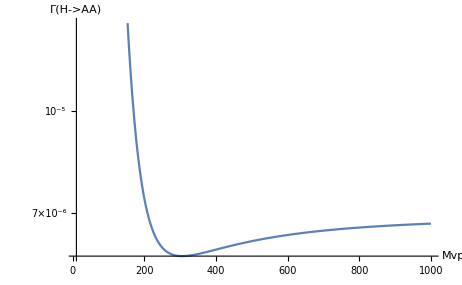

```mathematica
Block[{vv=243,MH=125,Mt=172.5,MW=80.385,Mb=4.25,Mc=1.23,Mtau=1.777,MV1=10,MVP=200,GF=1.2057*10^-5,Nc=3,α=1/137,λL=1},LogPlot[Re[AnchoHAAV[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFtau[4*Mtau^2/MH^2],XW[4*MW^2/MH^2],XV[4*MVP^2/MH^2],AO[MVP],BO[MH,MVP,MVP]]],{MVP,10,1000},AxesLabel->{"Mvp","Γ(H->AA)"}]]
```